# Versuch C1

```mathematica
ClearAll["Global`*"]
```

## Plot Settings

```mathematica
pltsettings={Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15],GridLines->Automatic,GridLinesStyle->Directive[Gray,Thickness[0.002],Opacity[0.8]]};
```

## Import Data

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]];
```

```mathematica
temps=ToExpression[StringSplit[StringSplit[#,"="][[-1]],"."][[1]]]&/@files;
```

```mathematica
data=Import[#][[1]]&/@files;
```

## Plotting

{Fest, Gemischt, Flüssig}

```mathematica
colours={RGBColor[0,0.6,0], RGBColor[0.56,0.37,0.60],Blue}
```

{RGBColor[0, 0.6, 0],RGBColor[0.56, 0.37, 0.6],RGBColor[0, 0, 1]}

```mathematica
states={"Fest", "Gemischt","Flüssig"}
```

{Fest,Gemischt,Flüssig}

```mathematica
assoc=AssociationThread[states,colours];
```

```mathematica
cf[_,_]=Black;
```

```mathematica
Do[cf[data[[i,j,1]],data[[i,j,2]]]=assoc[data[[i,j,3]]],{i,1,Length[data]},{j,1,Length[data[[i]]]}]
```

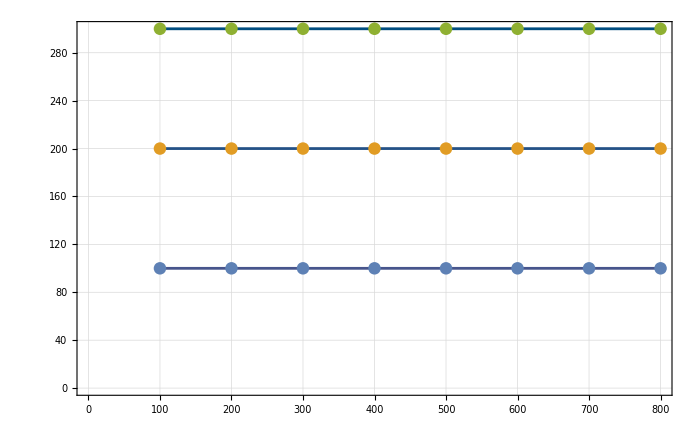

```mathematica
Show[ListPlot[Map[#[[1;;2]]&, data,{2}],ColorFunction->cf,ColorFunctionScaling->False,Joined->True],ListPlot[Map[#[[1;;2]]&, data,{2}],ColorFunction->cf,ColorFunctionScaling->False],pltsettings]
```

```mathematica
ListPlot[Map[#[[1;;2]]&, data,{2}],PlotStyle->ColorData["ThermometerColors"]/@Rescale[temps],pltsettings,Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.02]},PlotRange->All,PlotLegends->BarLegend[{ColorData["ThermometerColors"],{Min[temps],Max[temps]}},LabelStyle->Directive[Black,15],Method->{FrameStyle->Thickness[0.003],TicksStyle->Directive[Black,Thickness[0.003]]}]]
```

-Graphics-